```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
```

## Some perturbation theory tests

## Checking perturbation theory

```mathematica
Clear[z0,z,rhoM,ρM,TEST1]

Clear[ρV,rhoV]
NA=6.02214076*^23;(*Avagadro Zahl*)
kb=1.38066*^-23; (*Boltzmannkonstante*)
MN2=28.0134*10^-3; (*Molare masse N2*)
MO2=2*15.9994*10^-3; (*Molare Masse O2*)
press=2*10^-4*100 ;(*Druck in Pa, 1mbar = 100 Pa*)
T=300;
ρN2=(MN2*press)/(kb*NA*T)*kg2MeV/(m2invMeV^3);(*density of pure Subscript[N, 2] gas*)
ρO2=(MO2*press)/(kb*NA*T)*kg2MeV/(m2invMeV^3); (*density of pure Subscript[O, 2] gas*)
ρV=SetPrecision[0.8*ρN2+0.2*ρO2,1000]; (*Vacuum density*)

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]
ρM=rhoM;

CPrec=200;
constants=SetPrecision[{hbar->1.05457*^-34,c0->2.997925*^8,ec->1.602177*^-19},5 CPrec];
(* Note that ec is the unitless(!!) value of the electric charge, which is used to convert eV to J. ev=ec*J *)

m2invMeV  =1/(hbar c0/(1*^6*ec))/.constants; (*to be read as convert meter to MeV^-1*)
kg2MeV       =1/(ec 10^6/(c0^2))/.constants; 
s2invMeV  =1/(hbar/(1*^6 ec))/.constants; 
N2invMeV2=kg2MeV m2invMeV/s2invMeV^2; (*Newton to inverse MeV^2*)
kgm32MeV4=kg2MeV/m2invMeV^3; (*to be read as kg/m^3 converted to MeV^4 / density to natural units*)


Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]
Q[R_,ρ_,A_,λ_,β_]:=If[μ[A,λ,β,ρ] R<100,3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R) Tanh[SetPrecision[μ[A,λ,β,ρ] R,1000]])/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ] Tanh[μ[A,λ,β,ρ] R]),3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R))/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ])]

RealPhi0[λ_,A2_,β_]:=√((2 mpl^2)/(A2(ρM-ρV))(Veff[ϕρ[A2,λ,β,ρM],A2,λ,β,ρM]-Veff[ϕρ[A2,λ,β,ρV],A2,λ,β,ρV]))

ϕ0I[λ_,ρ_,A2_,β_]:=SetPrecision[(μ[A2,λ,β,ρV]*ϕM[A2,λ,β,ρV]+μ[A2,λ,β,ρ]*ϕM[A2,λ,β,ρ])/(μ[A2,λ,β,ρV]+μ[A2,λ,β,ρ]),5CPrec];

ϕI[λ_,ρ_,A2_,β_,z_]:=SetPrecision[Piecewise[{{ϕM[A2,λ,β,ρV]+(ϕ0I[λ,ρ,A2,β]-ϕM[A2,λ,β,ρV])E^SetPrecision[-μ[A2,λ,β,ρV]z,5CPrec],z>=0},{ϕM[A2,λ,β,ρ]+(ϕ0I[λ,ρ,A2,β]-ϕM[A2,λ,β,ρ])E^SetPrecision[μ[A2,λ,β,ρ]z,5CPrec],z<0}}],5CPrec];

Clear[z0,z,rhoM,ρM]

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]
ρM=rhoM;

CPrec=200;

RnF:=SetPrecision[0.5*10^-15*m2invMeV ,5CPrec] (*radius for fermi screening*)

RnM:=SetPrecision[5.9*10^-6*m2invMeV ,5CPrec] (*radius for micron screening*)

ρnF:=SetPrecision[m/((4π)/3 RnF^3) ,5CPrec] (*density for fermi screening*)

ρnM:=SetPrecision[m/((4π)/3 RnM^3) ,5CPrec] (*density for micron screening*)

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]

m:=SetPrecision[939.565346 ,5CPrec]  (*MeV*)
h:=1
g:=SetPrecision[9.80665*10^15/197.3269631*(197.3269631/(299792458*10^15))^2  ,5CPrec](*MeV*)
L:=SetPrecision[28*10^-6*10^15/197.3269631,5CPrec](*MeV^-1*)
z0:=SetPrecision[(h^2/(2 m^2 g))^(1/3),5CPrec] 
zE[T_]:=SetPrecision[T/(m g),5CPrec]
T1[n_]:=SetPrecision[m*g*(-z0*AiryAiZero[n]),5CPrec]
ξ[z_,T_]:=SetPrecision[(z - zE[T])/z0,5CPrec]
K1[n_]:=1/(SetPrecision[AiryAiPrime[SetPrecision[AiryAiZero[n],5CPrec]],5CPrec])

ψ1[z_,n_]:=SetPrecision[K1[n] AiryAi[ξ[z,T1[n]]],5CPrec]

E1=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[1],1000]];(*First energy level in MeV*);
E4=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[4],1000]];(*Fourth energy level in MeV*);
(* I check that the individual energy shifts: E1'/E1 <0.1 (energy correction divided by original energy) same for E4*)


mm=SetPrecision[0.001*m2invMeV,1000]; (*1mm in MeV*)
RangeV2[λ_,A2_,β_]:=SetPrecision[1/μ[A2,λ,β,ρV]/(ddr/10),1000]
RangeV3[λ_,A2_,β_]:=SetPrecision[1/μ[A2,λ,β,ρV]/(mm),1000] (*range in mm*)

EnergyDiffFSingle[n1_,λ_,A2_,β_]:=Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*NIntegrate[(ψ1[z*z0,n1]^2 )*((ϕI[λ,ρM,A2,β,z*z0])^2),{z,0,∞},WorkingPrecision->30,PrecisionGoal->15,AccuracyGoal->Infinity]
EnergyDiffFSingle2[n1_,λ_,A2_,β_]:=Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*NIntegrate[(ψ1[z*z0,n1]^2 )*((ϕI[λ,ρM,A2,β,z*z0])^2),{z,0,∞},WorkingPrecision->30,PrecisionGoal->15,AccuracyGoal->Infinity]

Energy1[n1_,λ_,A2_,β_]:=Abs[EnergyDiffFSingle[n1,λ,A2,β]]
Energy2[n1_,λ_,A2_,β_]:=Abs[EnergyDiffFSingle2[n1,λ,A2,β]]

TEST1[λ_,A2_,β_]:=Abs[(Energy1[1,λ,A2,β]-Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*ϕ0I[λ,ρM,A2,β]^2)/E1] (*Fermi screening*)
TEST2[λ_,A2_,β_]:=Abs[(Energy2[1,λ,A2,β]-Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*ϕ0I[λ,ρM,A2,β]^2)/E1] (*Micron screening*)


EnergyMIN2[n1_,n2_,λ_,A2_,β_]:=If[RangeV2[λ,A2,β]>10^3,0,
If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,

Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2)]]

EnergyDiffM[n1_,n2_,λ_,A2_,β_]:=If[RangeV2[λ,A2,β]>10^3,0,
If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,

Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)*NIntegrate[(ψ1[z*z0,n1]^2 - ψ1[z*z0,n2]^2)*(((ϕI[λ,ρM,A2,β,z*z0])^2-ϕM[A2,λ,β,ρM]^2)/(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)),{z,0,∞},WorkingPrecision->30,PrecisionGoal->3]]]

EnergyDiffM[n1_,n2_,λ_,A2_,β_]:=If[TEST2[λ,A2,β]>0.1,0,
If[RangeV2[λ,A2,β]>10^3,0,
If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,

Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)*NIntegrate[(ψ1[z*z0,n1]^2 - ψ1[z*z0,n2]^2)*(((ϕI[λ,ρM,A2,β,z*z0])^2-ϕM[A2,λ,β,ρM]^2)/(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)),{z,0,∞},WorkingPrecision->30,PrecisionGoal->3]]]]

EnergyDiffF[n1_,n2_,λ_,A2_,β_]:=If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,
If[RangeV2[λ,A2,β]>10^3,0,

Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)*NIntegrate[(ψ1[z*z0,n1]^2 - ψ1[z*z0,n2]^2)*(((ϕI[λ,ρM,A2,β,z*z0])^2-ϕM[A2,λ,β,ρM]^2)/(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)),{z,0,∞},WorkingPrecision->30,PrecisionGoal->3]]]
```

```mathematica
(*FERMI SCREENING! auskommentiert, damit nicht versehentlich aktiviert*)
Clear[β1RoughNew,β1RoughTest,A2,λ,β];
β=SetPrecision[1,1000];
β1Rough={};
β1RoughNew={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[28,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[35,5 CPrec];
Amin=SetPrecision[35,5 CPrec];
Amax=SetPrecision[44,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmin+iλ*λIncrement;
A2=10^At;
λ=10^λt;


AppendTo[β1RoughNew,{λt,At,TEST1[λ,A2,β]}]]]],iA];

DumpSave["β1RoughTest.mx",β1RoughTest];
```

## Derivation of exclusion plots

## Definitions etc

```mathematica
Clear[z0,z,rhoM,ρM,TEST1]

Clear[ρV,rhoV]
NA=6.02214076*^23;(*Avagadro Zahl*)
kb=1.38066*^-23; (*Boltzmannkonstante*)
MN2=28.0134*10^-3; (*Molare masse N2*)
MO2=2*15.9994*10^-3; (*Molare Masse O2*)
press=2*10^-4*100 ;(*Druck in Pa, 1mbar = 100 Pa*)
T=300;
ρN2=(MN2*press)/(kb*NA*T)*kg2MeV/(m2invMeV^3);(*density of pure Subscript[N, 2] gas*)
ρO2=(MO2*press)/(kb*NA*T)*kg2MeV/(m2invMeV^3); (*density of pure Subscript[O, 2] gas*)
ρV=SetPrecision[0.8*ρN2+0.2*ρO2,1000]; (*Vacuum density*)

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]
ρM=rhoM;

CPrec=200;
constants=SetPrecision[{hbar->1.05457*^-34,c0->2.997925*^8,ec->1.602177*^-19},5 CPrec];
(* Note that ec is the unitless(!!) value of the electric charge, which is used to convert eV to J. ev=ec*J *)

m2invMeV  =1/(hbar c0/(1*^6*ec))/.constants; (*to be read as convert meter to MeV^-1*)
kg2MeV       =1/(ec 10^6/(c0^2))/.constants; 
s2invMeV  =1/(hbar/(1*^6 ec))/.constants; 
N2invMeV2=kg2MeV m2invMeV/s2invMeV^2; (*Newton to inverse MeV^2*)
kgm32MeV4=kg2MeV/m2invMeV^3; (*to be read as kg/m^3 converted to MeV^4 / density to natural units*)


Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]
Q[R_,ρ_,A_,λ_,β_]:=If[μ[A,λ,β,ρ] R<100,3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R) Tanh[SetPrecision[μ[A,λ,β,ρ] R,1000]])/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ] Tanh[μ[A,λ,β,ρ] R]),3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R))/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ])]

RealPhi0[λ_,A2_,β_]:=√((2 mpl^2)/(A2(ρM-ρV))(Veff[ϕρ[A2,λ,β,ρM],A2,λ,β,ρM]-Veff[ϕρ[A2,λ,β,ρV],A2,λ,β,ρV]))

ϕ0I[λ_,ρ_,A2_,β_]:=SetPrecision[(μ[A2,λ,β,ρV]*ϕM[A2,λ,β,ρV]+μ[A2,λ,β,ρ]*ϕM[A2,λ,β,ρ])/(μ[A2,λ,β,ρV]+μ[A2,λ,β,ρ]),5CPrec];

ϕI[λ_,ρ_,A2_,β_,z_]:=SetPrecision[Piecewise[{{ϕM[A2,λ,β,ρV]+(ϕ0I[λ,ρ,A2,β]-ϕM[A2,λ,β,ρV])E^SetPrecision[-μ[A2,λ,β,ρV]z,5CPrec],z>=0},{ϕM[A2,λ,β,ρ]+(ϕ0I[λ,ρ,A2,β]-ϕM[A2,λ,β,ρ])E^SetPrecision[μ[A2,λ,β,ρ]z,5CPrec],z<0}}],5CPrec];

Clear[z0,z,rhoM,ρM]

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]
ρM=rhoM;

CPrec=200;

RnF:=SetPrecision[0.5*10^-15*m2invMeV ,5CPrec] (*radius for fermi screening*)

RnM:=SetPrecision[5.9*10^-6*m2invMeV ,5CPrec] (*radius for micron screening*)

ρnF:=SetPrecision[m/((4π)/3 RnF^3) ,5CPrec] (*density for fermi screening*)

ρnM:=SetPrecision[m/((4π)/3 RnM^3) ,5CPrec] (*density for micron screening*)

rhoM:=SetPrecision[1.082*10^-5 ,5CPrec]

m:=SetPrecision[939.565346 ,5CPrec]  (*MeV*)
h:=1
g:=SetPrecision[9.80665*10^15/197.3269631*(197.3269631/(299792458*10^15))^2  ,5CPrec](*MeV*)
L:=SetPrecision[28*10^-6*10^15/197.3269631,5CPrec](*MeV^-1*)
z0:=SetPrecision[(h^2/(2 m^2 g))^(1/3),5CPrec] 
zE[T_]:=SetPrecision[T/(m g),5CPrec]
T1[n_]:=SetPrecision[m*g*(-z0*AiryAiZero[n]),5CPrec]
ξ[z_,T_]:=SetPrecision[(z - zE[T])/z0,5CPrec]
K1[n_]:=1/(SetPrecision[AiryAiPrime[SetPrecision[AiryAiZero[n],5CPrec]],5CPrec])

ψ1[z_,n_]:=SetPrecision[K1[n] AiryAi[ξ[z,T1[n]]],5CPrec] (*NOT normalized*)

ψ[z_,n_]:=(√m2invMeV)/(√z0)SetPrecision[K1[n] AiryAi[ξ[z*m2invMeV,T1[n]]],5CPrec] (*normalized wave function in SI units*)

E1=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[1],1000]];(*First energy level in MeV*);
E2=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[2],1000]];
E3=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[3],1000]];
E4=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[4],1000]];(*Fourth energy level in MeV*);
En[n_]:=Abs[((m*g^2)/2)^(1/3)*SetPrecision[AiryAiZero[n],1000]]
(* I check that the individual energy shifts: E1'/E1 <0.1 (energy correction divided by original energy) same for E4*)


mm=SetPrecision[0.001*m2invMeV,1000]; (*1mm in MeV*)
RangeV2[λ_,A2_,β_]:=SetPrecision[1/μ[A2,λ,β,ρV]/(ddr/10),1000]
RangeV3[λ_,A2_,β_]:=SetPrecision[1/μ[A2,λ,β,ρV]/(mm),1000] (*range in mm*)

EnergyDiffFSingle[n1_,λ_,A2_,β_]:=Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*NIntegrate[(ψ1[z*z0,n1]^2 )*((ϕI[λ,ρM,A2,β,z*z0])^2-(ϕI[λ,ρM,A2,β,0*z0])^2),{z,0,∞},WorkingPrecision->30,PrecisionGoal->15,AccuracyGoal->Infinity]
EnergyDiffFSingle2[n1_,λ_,A2_,β_]:=Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*NIntegrate[(ψ1[z*z0,n1]^2 )*((ϕI[λ,ρM,A2,β,z*z0])^2-(ϕI[λ,ρM,A2,β,0*z0])^2),{z,0,∞},WorkingPrecision->30,PrecisionGoal->15,AccuracyGoal->Infinity]

Energy1[n1_,λ_,A2_,β_]:=Abs[EnergyDiffFSingle[n1,λ,A2,β]]
Energy2[n1_,λ_,A2_,β_]:=Abs[EnergyDiffFSingle2[n1,λ,A2,β]]

TEST1[λ_,A2_,β_]:=Abs[Energy1[1,λ,A2,β]/E1] (*Fermi screening*)
TEST2[λ_,A2_,β_]:=Abs[Energy2[1,λ,A2,β]/E1] (*Micron screening*)


EnergyMIN2[n1_,n2_,λ_,A2_,β_]:=If[RangeV2[λ,A2,β]>10^3,0,
If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,

Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2)]]

EnergyDiffM[n1_,n2_,λ_,A2_,β_]:=If[RangeV2[λ,A2,β]>10^3,0,
If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,

Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)*NIntegrate[(ψ1[z*z0,n1]^2 - ψ1[z*z0,n2]^2)*(((ϕI[λ,ρM,A2,β,z*z0])^2-ϕM[A2,λ,β,ρM]^2)/(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)),{z,0,∞},WorkingPrecision->30,PrecisionGoal->5]]]

EnergyDiffF[n1_,n2_,λ_,A2_,β_]:=If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,
If[RangeV2[λ,A2,β]>10^3,0,

Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)*NIntegrate[(ψ1[z*z0,n1]^2 - ψ1[z*z0,n2]^2)*(((ϕI[λ,ρM,A2,β,z*z0])^2-ϕM[A2,λ,β,ρM]^2)/(ϕM[A2,λ,β,ρV]^2-ϕM[A2,λ,β,ρM]^2)),{z,0,∞},WorkingPrecision->30,PrecisionGoal->5]]]

(*The following functions creates the necessary matrices to compute the eigenvalues and eigenvectors of the schrödinger equation for fermi screening, I used the algorithm from the paper "A self-consistent solution of Schrödinger-Poisson equations using a nonuniform mesh" to use a finite difference scheme with a
non uniform mesh*)

GetMatricesM[λ_,A2_,β_,Cutoff1_,Cutoff2_,POINTS1_,POINTS2_]:=Block[{maxMeshSize1,maxMeshSize2,points1,points2,points,h,L2,h0,hn,FAKTOR,L1,Ln,T,ROW,M,L,Newton,Dilaton,B,H},

maxMeshSize1=Cutoff1/POINTS1; (*nur bis 100 mu meter*)
maxMeshSize2=Cutoff2/POINTS2; (*nur bis 100 mu meter*)
points1=SetPrecision[Table[i*maxMeshSize1,{i,0,POINTS1}],100];
points2=SetPrecision[Table[i*maxMeshSize2,{i,0,POINTS2}],100];
points=SetPrecision[Sort[Join[points1,points2]],5CPrec];
points=DeleteCases[DeleteCases[points,0],Cutoff1];
points=DeleteDuplicates[points];
(*first I define h as in the paper and define Subscript[L, i], note that L as defined actually containts Subscript[L, i]^2*)
h={};
L2={};
h0:=points[[1]];
hn:=points[[-1]]-points[[-2]];

For[i=1, i<=Length[points]-1,i++,
AppendTo[h,(points[[i+1]]-points[[i]])]];
AppendTo[h,hn];
FAKTOR=-1/(2*m*m2invMeV^2);
L1:=(h[[1]]+h0)/2;
Ln:=(h[[-1]]+h[[-1]])/2;
AppendTo[L2,L1];
For[i=2, i<=Length[points]-1,i++,
AppendTo[L2,((h[[i]]+h[[i-1]])/2)]];

AppendTo[L2,Ln];

(*Next I define the kinetic matrix, which is a in the paper without the potential, here denoted by T*)

T={};
(*The first line is an exeption because of the boundary condition at Subscript[x, 0]= 0*)
Clear[ROW];
ROW={};
AppendTo[ROW,-FAKTOR*(1/(h[[1]]*L2[[1]])+1/(h0*L2[[1]]))];
AppendTo[ROW,FAKTOR*(1/(h[[1]]*L2[[1]]))];
For[j=3,j<=Length[points],j++,
AppendTo[ROW,0];
];

AppendTo[T,ROW];

(*Now all rows exept for the last one are computed*)

For[i=2,i<=Length[points]-1,i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,-FAKTOR*1/(h[[i]]*L2[[i]])-FAKTOR*1/(h[[i-1]]*L2[[i]]),If[j==i+1,FAKTOR*1/(h[[i]]*L2[[i]]),If[j==i-1,FAKTOR*1/(h[[i-1]]*L2[[i]]),0]]]
]];
AppendTo[T,ROW]]

(*The last row is still missing and defined by the second boundary condition *);
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,0];
];
ROW[[-2]]=FAKTOR*1/(h[[-2]]*L2[[-1]]);
ROW[[-1]]=-FAKTOR*(1/(h[[-2]]*L2[[-1]])+1/(h[[-1]]*L2[[-1]]));
AppendTo[T,ROW];

(*Next I define the Matrix M and B in the paper*)

M=DiagonalMatrix[L2];

L=DiagonalMatrix[Sqrt[L2]];


(*Next I define the Newtonian potential operator*)
Newton={};
For[i=1,i<=Length[points],i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,m*g*m2invMeV*points[[i]],0]]
];
AppendTo[Newton,ROW]];

Dilaton={};
For[i=1,i<=Length[points],i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2*mpl^2)*(ϕI[λ,ρM,A2,β,points[[i]]*m2invMeV])^2-Q[RnM,ρnM,A2,λ,β]*(A2*m)/(2 mpl^2)*ϕ0I[λ,ρM,A2,β]^2,0]]
];
AppendTo[Dilaton,ROW]];

B=SetPrecision[M.(T+Newton+Dilaton),30];

H=Inverse[L].B.Inverse[L];
{points,H,L}] (*Note that this is not actually the Hamilton! the Eigenvectos still have to be multiplied by L^-1(!)*)

GetMatricesF[λ_,A2_,β_,Cutoff1_,Cutoff2_,POINTS1_,POINTS2_]:=Block[{maxMeshSize1,maxMeshSize2,points1,points2,points,h,L2,h0,hn,FAKTOR,L1,Ln,T,ROW,M,L,Newton,Dilaton,B,H},

maxMeshSize1=Cutoff1/POINTS1; (*nur bis 100 mu meter*)
maxMeshSize2=Cutoff2/POINTS2; (*nur bis 100 mu meter*)
points1=SetPrecision[Table[i*maxMeshSize1,{i,0,POINTS1}],100];
points2=SetPrecision[Table[i*maxMeshSize2,{i,0,POINTS2}],100];
points=SetPrecision[Sort[Join[points1,points2]],5CPrec];
points=DeleteCases[DeleteCases[points,0],Cutoff1];
points=DeleteDuplicates[points];
(*first I define h as in the paper and define Subscript[L, i], note that L as defined actually containts Subscript[L, i]^2*)
h={};
L2={};
h0:=points[[1]];
hn:=points[[-1]]-points[[-2]];

For[i=1, i<=Length[points]-1,i++,
AppendTo[h,(points[[i+1]]-points[[i]])]];
AppendTo[h,hn];
FAKTOR=-1/(2*m*m2invMeV^2);
L1:=(h[[1]]+h0)/2;
Ln:=(h[[-1]]+h[[-1]])/2;
AppendTo[L2,L1];
For[i=2, i<=Length[points]-1,i++,
AppendTo[L2,((h[[i]]+h[[i-1]])/2)]];

AppendTo[L2,Ln];

(*Next I define the kinetic matrix, which is a in the paper without the potential, here denoted by T*)

T={};
(*The first line is an exeption because of the boundary condition at Subscript[x, 0]= 0*)
Clear[ROW];
ROW={};
AppendTo[ROW,-FAKTOR*(1/(h[[1]]*L2[[1]])+1/(h0*L2[[1]]))];
AppendTo[ROW,FAKTOR*(1/(h[[1]]*L2[[1]]))];
For[j=3,j<=Length[points],j++,
AppendTo[ROW,0];
];

AppendTo[T,ROW];

(*Now all rows exept for the last one are computed*)

For[i=2,i<=Length[points]-1,i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,-FAKTOR*1/(h[[i]]*L2[[i]])-FAKTOR*1/(h[[i-1]]*L2[[i]]),If[j==i+1,FAKTOR*1/(h[[i]]*L2[[i]]),If[j==i-1,FAKTOR*1/(h[[i-1]]*L2[[i]]),0]]]
]];
AppendTo[T,ROW]]

(*The last row is still missing and defined by the second boundary condition *);
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,0];
];
ROW[[-2]]=FAKTOR*1/(h[[-2]]*L2[[-1]]);
ROW[[-1]]=-FAKTOR*(1/(h[[-2]]*L2[[-1]])+1/(h[[-1]]*L2[[-1]]));
AppendTo[T,ROW];

(*Next I define the Matrix M and B in the paper*)

M=DiagonalMatrix[L2];

L=DiagonalMatrix[Sqrt[L2]];


(*Next I define the Newtonian potential operator*)
Newton={};
For[i=1,i<=Length[points],i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,m*g*m2invMeV*points[[i]],0]]
];
AppendTo[Newton,ROW]];

Dilaton={};
For[i=1,i<=Length[points],i++,
Clear[ROW];
ROW={};
For[j=1,j<=Length[points],j++,
AppendTo[ROW,If[i==j,Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2*mpl^2)*(ϕI[λ,ρM,A2,β,points[[i]]*m2invMeV])^2-Q[RnF,ρnF,A2,λ,β]*(A2*m)/(2 mpl^2)*ϕ0I[λ,ρM,A2,β]^2,0]]
];
AppendTo[Dilaton,ROW]];

B=SetPrecision[M.(T+Newton+Dilaton),30];

H=Inverse[L].B.Inverse[L];
{points,H,L}] (*Note that this is not actually the Hamilton! the Eigenvectos still have to be multiplied by L^-1(!)*)
```

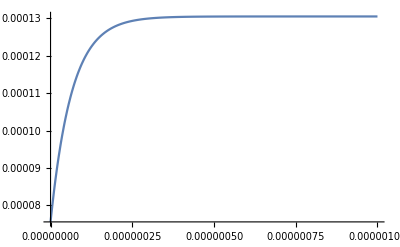

```mathematica
λ=10^27;
A2=10^45;
β=1;
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,10^-6},PlotRange->Full]
```

## Numerical solution of Schrödinger equation and computation of Eigenvalues and limits

### Checking that i can reproduce the analytical Newtonian result without Dilaton field - ok!

```mathematica
λ=10^SetPrecision[40,100];(*setting lamda that high effectively turns of the dilaton potential since it scales by 1/λ*)
A2=10^50;
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=150; (*Set number of points for equidistant grid*)
POINTS2=100;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigensystem[H];
```

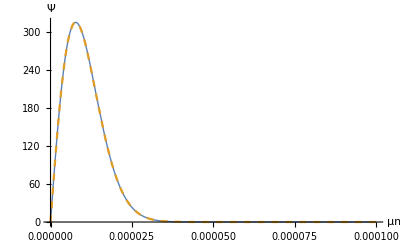

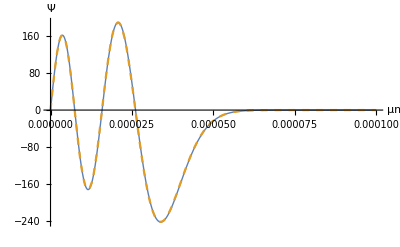

0.00038088544615483886178145389

0.00110261882354665893751131668

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{ψ[z,1],f1[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{ψ[z,4],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
(E1-EVS[[1]][[-1]])/E1
(E4-EVS[[1]][[-4]])/E4
```

### Checking that perturbation theory and the numerical solution match, where perturbation theory is valid - ok!

#### Micron screening

```mathematica
λ=10^SetPrecision[33,100];
A2=10^41;
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle2[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle2[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle2[1,λ,A2,β]-EnergyDiffFSingle2[4,λ,A2,β]
```

{1.565726191112758660559329168×10^-19,1.567451675410684296710015471×10^-19}

{1.690828028401936711202818476×10^-19,1.69619301984469071170400527439×10^-19}

-1.25101837289178050643489308×10^-20

-1.287413444340064149939898034×10^-20

```mathematica
λ=10^SetPrecision[30.5,100];
A2=10^SetPrecision[36,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle2[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle2[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle2[1,λ,A2,β]-EnergyDiffFSingle2[4,λ,A2,β]
```

{2.1146351504282907618137625567×10^-19,2.1152737540750011298357149549×10^-19}

{2.125375099509450027885126151×10^-19,2.13075054684506104725061935338×10^-19}

-1.0739949081159266071363595×10^-21

-1.54767927700599174149043985×10^-21

```mathematica
λ=10^33;
A2=10^24;
β=10^18;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle2[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle2[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle2[1,λ,A2,β]-EnergyDiffFSingle2[4,λ,A2,β]
```

{0.00156862464454854137815285459899,0.00156862464454854137823754989386}

{0.00156862464454854138661203566539,0.00156862464454854138715160616271}

-8.4591810664×10^-21

-8.91405626885×10^-21

```mathematica
λ=10^SetPrecision[30.5,100];
A2=10^21;
β=10^18;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle2[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle2[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle2[1,λ,A2,β]-EnergyDiffFSingle2[4,λ,A2,β]
```

{0.244528352663759855762936310519,0.244528352663759855766138475392}

{0.2445283526637598560091721033,0.244528352663759856017817359505}

-2.4623579278×10^-19

-2.5167888411×10^-19

#### Fermi screening

```mathematica
λ=10^SetPrecision[31.3,100];
A2=10^41;
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β]
```

{5.286936994279876886899071879×10^-20,5.29493704717368567263049120634×10^-20}

{5.75126471761296107505240542×10^-20,5.80501270819284269008448051942×10^-20}

-4.6432772333308418815333354×10^-21

-5.100756610191570174539893131×10^-21

```mathematica
λ=10^SetPrecision[30.5,100];
A2=10^36;
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β]
```

{1.7647136073105461826726940789×10^-19,1.76535172874316969100659817893×10^-19}

{1.772894855585846866207194629×10^-19,1.77826825211012879871486978085×10^-19}

-8.1812482753006835345005501×10^-22

-1.29165233669591077082716019×10^-21

```mathematica
λ=10^SetPrecision[30.5,100];
A2=10^20;
β=10^18;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β]
```

{0.010575782698309780848922602264,0.0105757826983097808489870937649}

{0.0105757826983097808520508209473,0.0105757826983097808525906724165}

-3.1282186834×10^-21

-3.6035786516×10^-21

```mathematica
λ=10^SetPrecision[31,100];
A2=10^24;
β=10^18;
Cutoff1=100*10^-6;
Cutoff2=100*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=1;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];

EVS=Eigenvalues[H];
{EVS[[-1]]-E1,EnergyDiffFSingle[1,λ,A2,β]}
{EVS[[-4]]-E4,EnergyDiffFSingle[4,λ,A2,β]}
EVS[[-1]]-E1-(EVS[[-4]]-E4)
EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β]
```

{0.00216251162315611457945642585194,0.00216251162315611457955949785173}

{0.00216251162315611459130747716121,0.00216251162315611459184844814831}

-1.18510513093×10^-20

-1.22889502966×10^-20

### Exclusion plot β = 1 - Fermi screening - compute correct points along exclusion line

```mathematica
(*I manually compute points along the contour of the exclusion plot - 2*10^-21 MeV, but I start with computing the exclusion area from perturbation theory*)
```

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotQ1=ContourPlot[EnergyDiffF[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15),{λ,Log10[10^20],Log10[10^33]},{A2,Log10[10^35],Log10[10^50]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.9,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})];
```

#### Compute points along ExclusionLine

```mathematica
λ=10^SetPrecision[31.0,100];
A2=10^SetPrecision[42.1,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

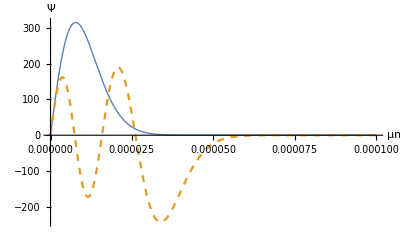

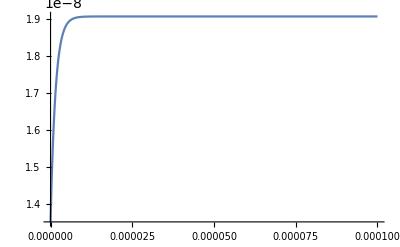

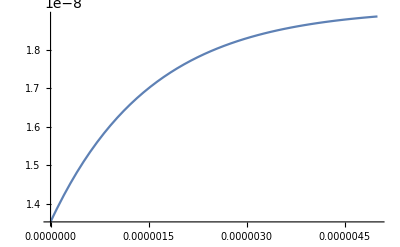

-1.1047707563256293278920316×10^-21

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)
```

```mathematica
λ=10^SetPrecision[30.0,100];
A2=10^SetPrecision[43.2,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

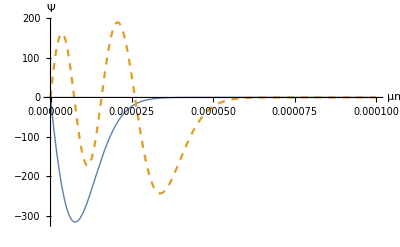

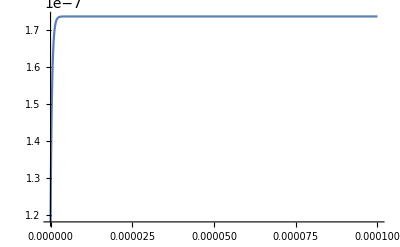

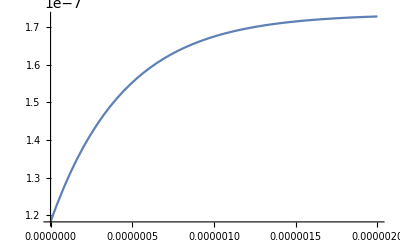

0.7835768596491112064592669

0.7434091099126490198086576

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[29.0,100];
A2=10^SetPrecision[45,100]; (*2*10^-21 is between 44.7 and 45*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

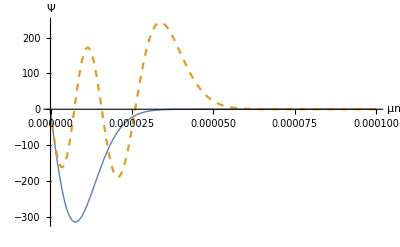

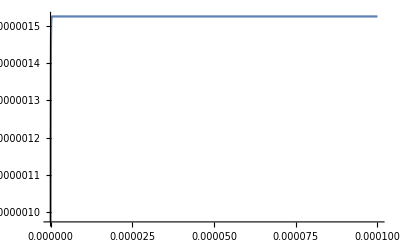

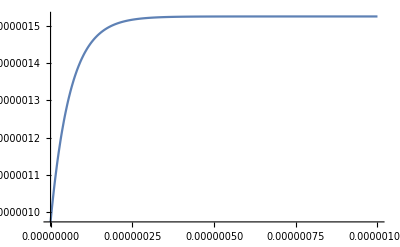

0.172092523218377133757

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
```

```mathematica
λ=10^SetPrecision[29.5,100];
A2=10^SetPrecision[44,100]; (*2*10^-21 is between 43.5 and 44*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

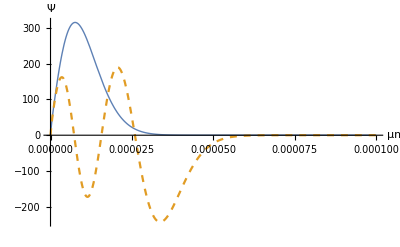

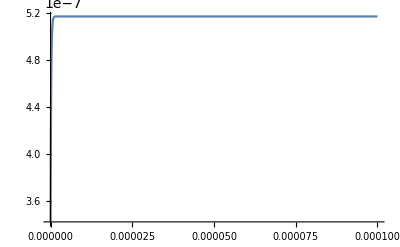

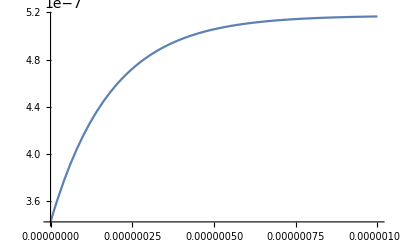

0.055866951691657643979604

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
```

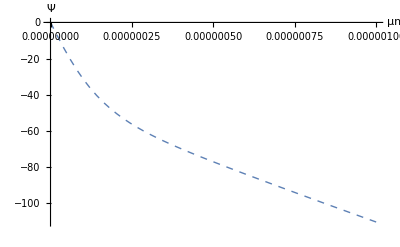

```mathematica
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}]
```

```mathematica
λ=10^SetPrecision[28.0,100];
A2=10^SetPrecision[47.5,100];(*2*10^-21 is between 47 and 47.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-7;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

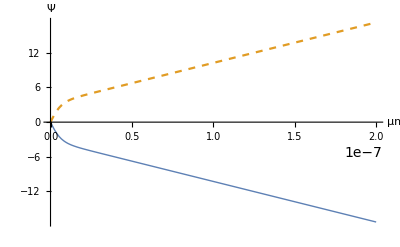

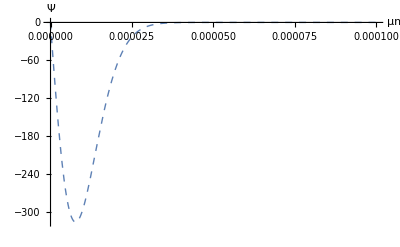

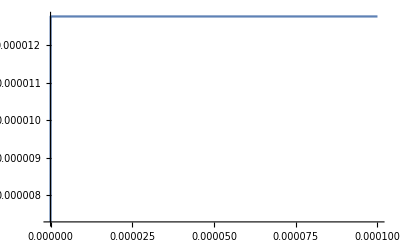

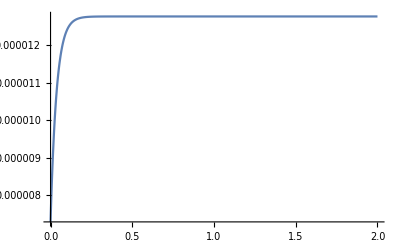

0.22535847360381692873

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
```

```mathematica
λ=10^SetPrecision[28.5,100];
A2=10^SetPrecision[46,100];(*2*10^-21 is between 45.5 and 46*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-7;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

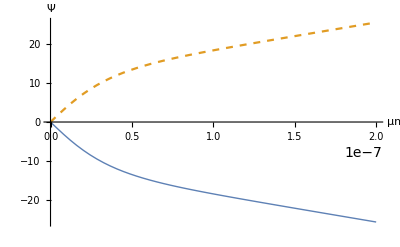

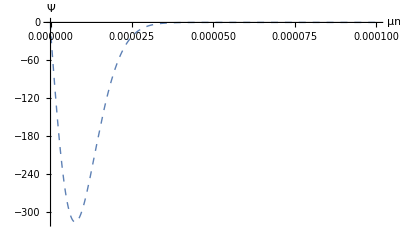

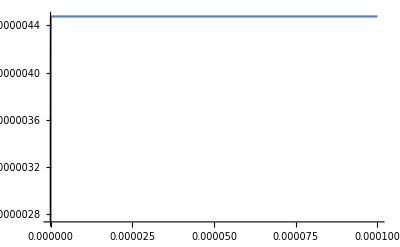

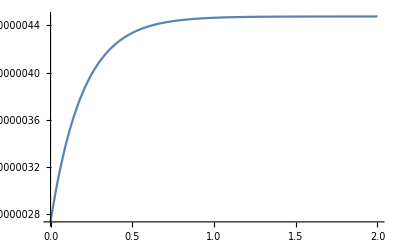

0.20268392292916287402

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
```

```mathematica
λ=10^SetPrecision[26.5,100];
A2=10^SetPrecision[50.5,100]; (*2*10^-21 is between 50 and 50.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-9;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

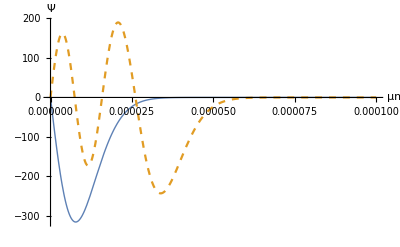

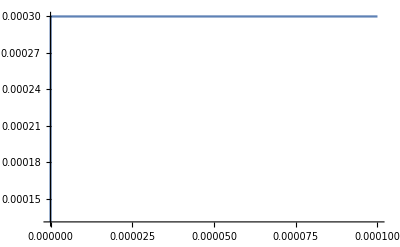

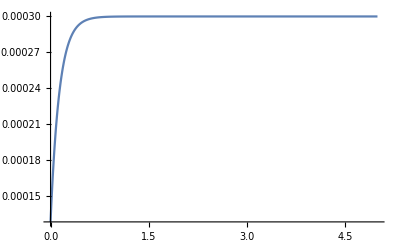

0.23555118945599892

7.1544×10^-13

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[27.0,100];
A2=10^SetPrecision[49.5,100]; (*2*10^-21 is between 49 and 49.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-9;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

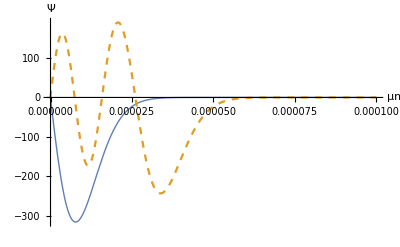

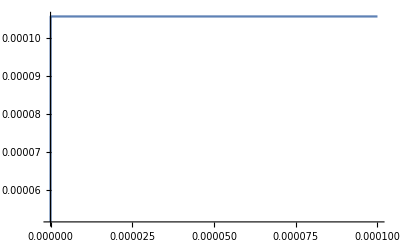

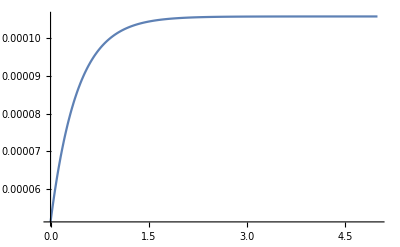

0.234592348156966032

5.153962932×10^-9

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[27.5,100];
A2=10^SetPrecision[49.1,100]; (*2*10^-21 is at ~49.1*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-9;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

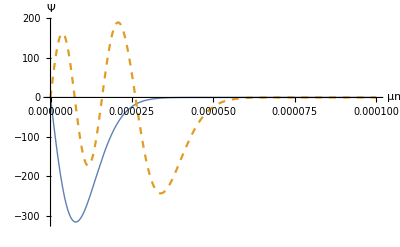

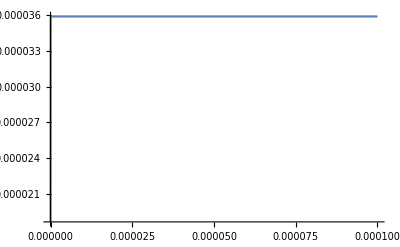

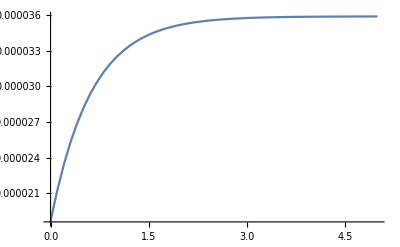

0.2357409397011047216

4.6711827203×10^-9

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

#### Final exclusion plot

{{31,42.1},{30,43.2},{29.5,44},{29,45},{28.5,46},{28,47.5},{27.5,49.1},{27,49.5},{26.5,50.5}}

InterpolatingFunction[…]

103.875-2.01548 x

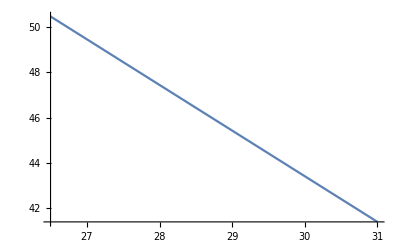

```mathematica
ExculsionLine={{31,42.1},{30,43.2},{29.5,44},{29,45},{28.5,46},{28,47.5},{27.5,49.1},{27,49.5},{26.5,50.5}}
f=Interpolation[ExculsionLine,InterpolationOrder->3]
f2=Fit[ExculsionLine,{1,x},x]
FIT[x_]:=103.87548387096768-2.015483870967738 x

Plot[FIT[λ],{λ,26.5,31}]
Clear[Exclude]
Exclude[λ_,A2_,β_]:=If[FIT[Log10[λ]]>Log10[A2]&&(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)<0.1,10,0]
```

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotQ2=ContourPlot[Exclude[10^λ,10^A2,β],{λ,Log10[10^20],Log10[10^31]},{A2,Log10[10^38],Log10[10^50]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.9,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})];
```

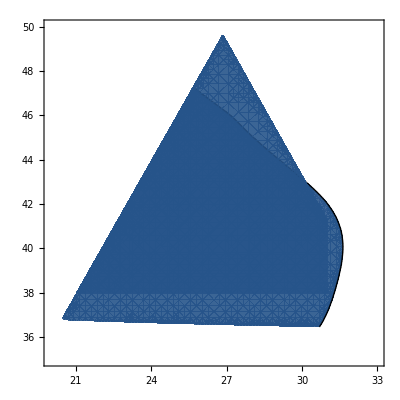

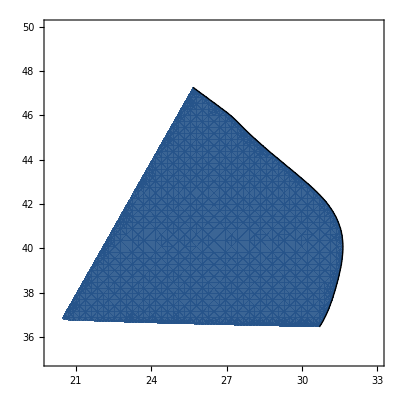

```mathematica
Fermi1=Show[PlotQ1,PlotQ2]
Show[PlotQ1]
```

### Exclusion plot β = 1 - Fermi screening second part (exp ~ 1)

#### Compute points along exclusion line

```mathematica
λ=10^SetPrecision[-1,100];
A2=10^SetPrecision[44.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=200; (*Set number of points for equidistant grid*)
POINTS2=200;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

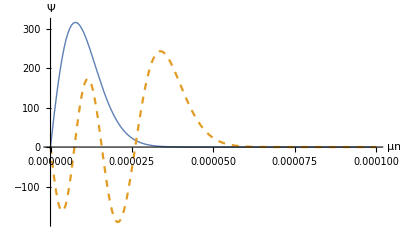

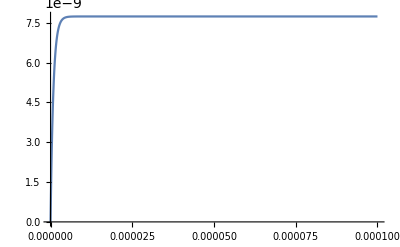

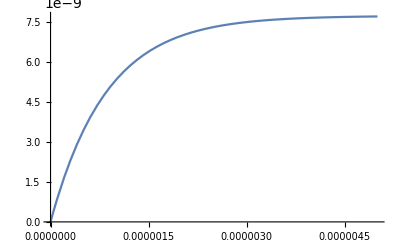

0.1534840023390870127902865

1.21851892854116117687079218

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[-0.5,100];
A2=10^SetPrecision[45,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

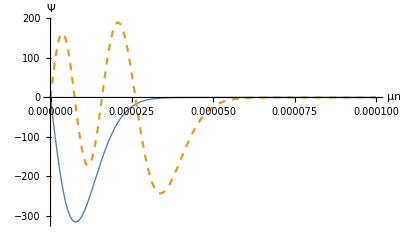

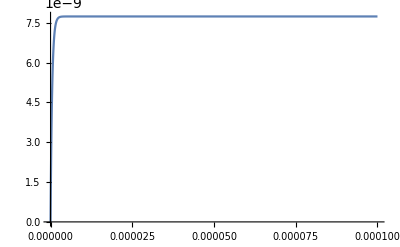

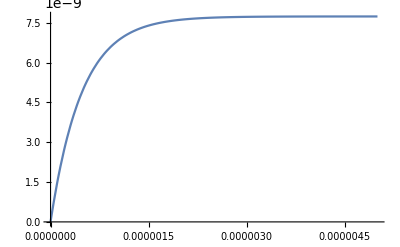

0.82389213328320600640471846

0.099749531213512257140914016

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

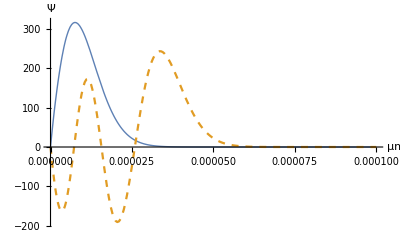

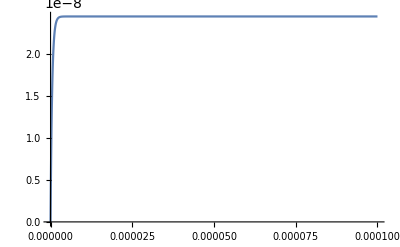

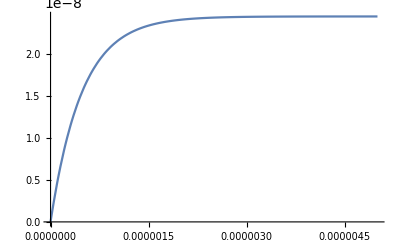

0.1309200908654553572133304

0.99749531213512257140914016

```mathematica
λ=10^SetPrecision[-0,100];
A2=10^SetPrecision[45,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=200; (*Set number of points for equidistant grid*)
POINTS2=200;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

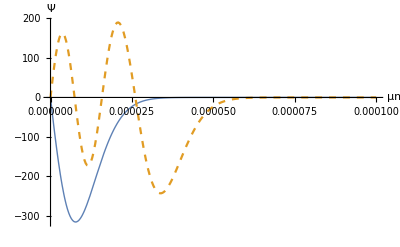

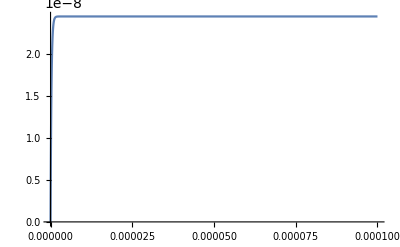

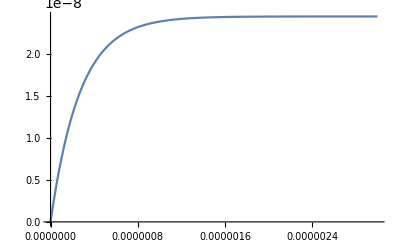

0.7516729104436652495173015

0.0648380611650607169688567

```mathematica
λ=10^SetPrecision[0.5,100];
A2=10^SetPrecision[45.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=3*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

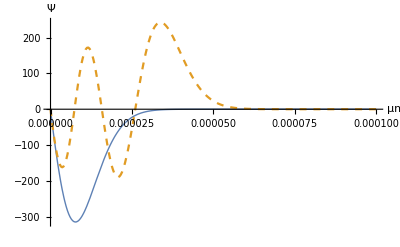

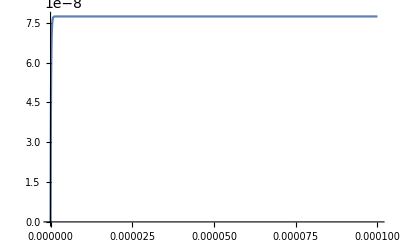

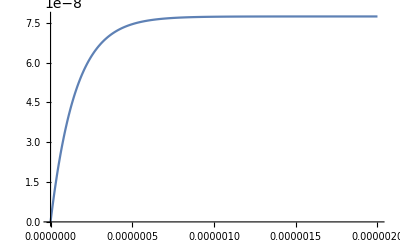

0.687981712610757512340455

0.038334482638110532102716

```mathematica
λ=10^SetPrecision[1.5,100];
A2=10^SetPrecision[46,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

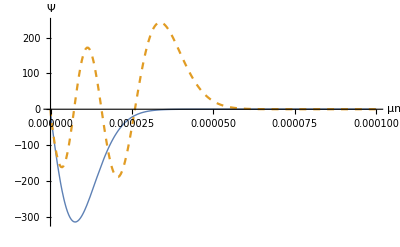

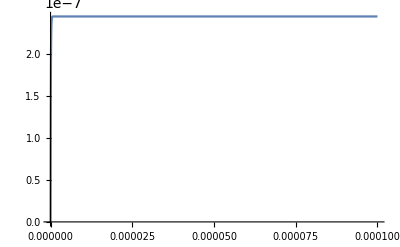

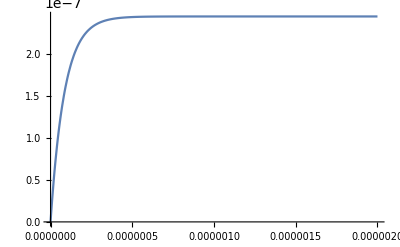

0.66296725048638032089901

0.02191526248438717837424

```mathematica
λ=10^SetPrecision[2.5,100];
A2=10^SetPrecision[46.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

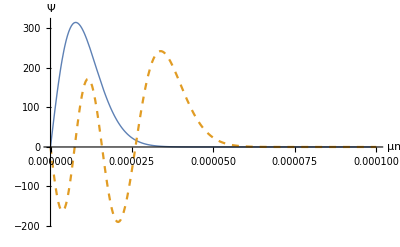

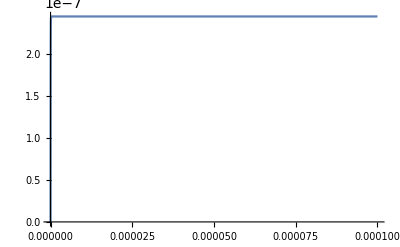

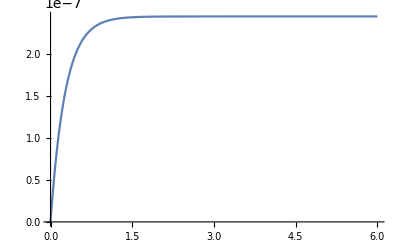

0.82338874723530547649943

0.00006978947826799433857

```mathematica
λ=10^SetPrecision[3.5,100];
A2=10^SetPrecision[47.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=6*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

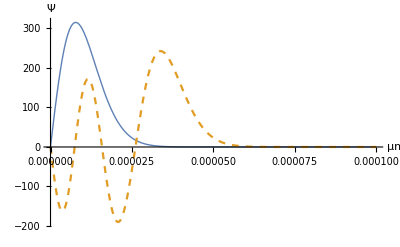

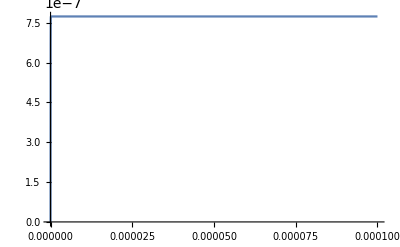

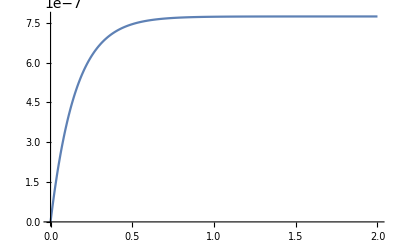

0.8849103021789197945189

0.0000392667747037085633

```mathematica
λ=10^SetPrecision[4.5,100];
A2=10^SetPrecision[48,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

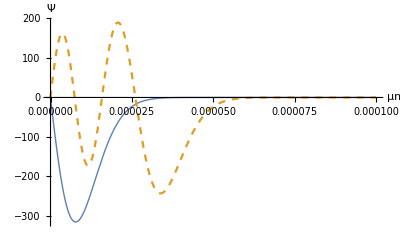

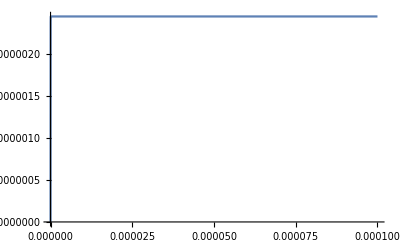

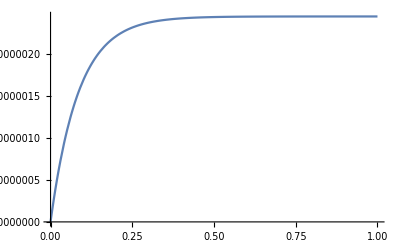

0.90340431635255055806

0.000022085155770768095

```mathematica
λ=10^SetPrecision[5.5,100];
A2=10^SetPrecision[48.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

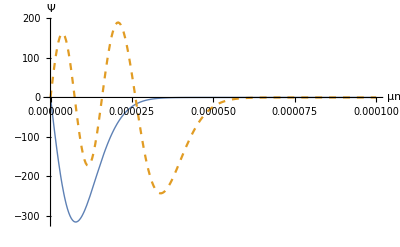

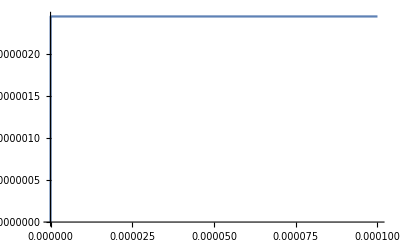

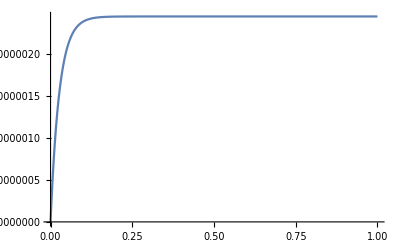

0.906510834184406429772

6.9844552443434×10^-8

```mathematica
λ=10^SetPrecision[6.5,100];
A2=10^SetPrecision[49.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

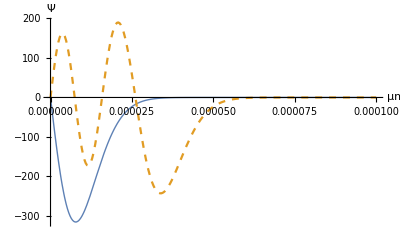

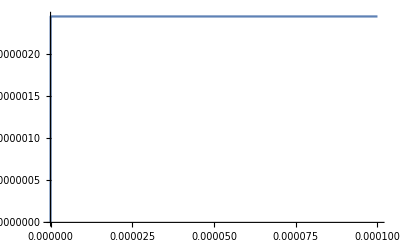

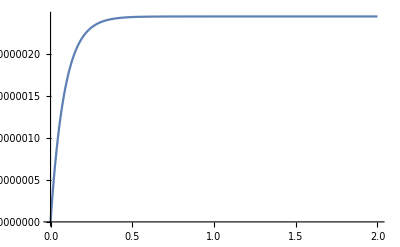

0.936898265657636150106

2.20871870747×10^-10

```mathematica
λ=10^SetPrecision[7.5,100];
A2=10^SetPrecision[50.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-8;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

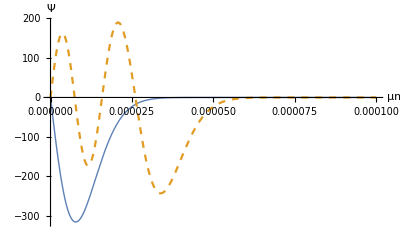

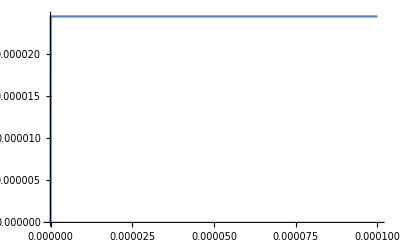

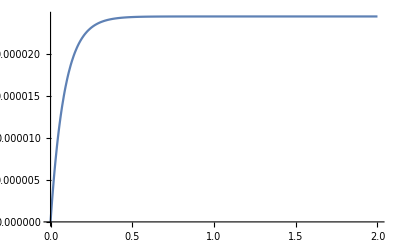

0.9365868659840362162

2.20871870747×10^-8

```mathematica
λ=10^SetPrecision[8.5,100];
A2=10^SetPrecision[50.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-8;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesF[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[(EnergyDiffFSingle[1,λ,A2,β]-EnergyDiffFSingle[4,λ,A2,β])/(2*10^-21)]
```

#### Final exclusion plot

{{-1,44.5},{-0.5,45},{0,45},{0.5,45.5},{1.5,46},{2.5,46.5},{3.5,47.5},{4.5,48},{5.5,48.5},{6.5,49.5},{7.5,50.5},{8.5,50.5}}

InterpolatingFunction[…]

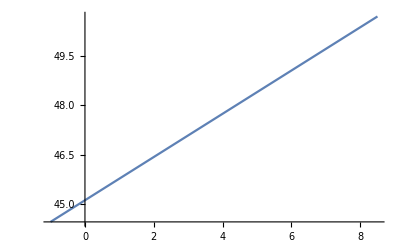

```mathematica
ExculsionLine={{-1,44.5},{-0.5,45},{0,45},{0.5,45.5},{1.5,46},{2.5,46.5},{3.5,47.5},{4.5,48},{5.5,48.5},{6.5,49.5},{7.5,50.5},{8.5,50.5}}
f=Interpolation[ExculsionLine,InterpolationOrder->3]
f2=Fit[ExculsionLine,{1,x},x];
FIT[x_]:=45.106531049250535+0.6595289079229121 x

Plot[FIT[λ],{λ,-1,8.5}]
Clear[Exclude]
Exclude[λ_,A2_,β_]:=If[FIT[Log10[λ]]>Log10[A2]&&(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)<0.1&&RangeV2[λ,A2,β]<10^3,10,0]
```

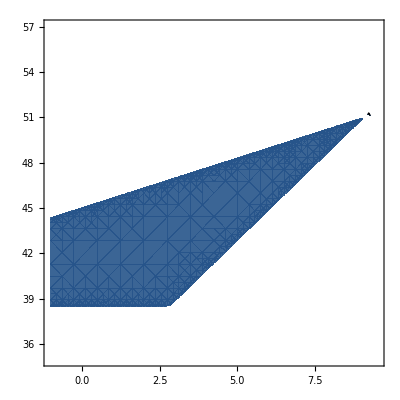

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotQC=ContourPlot[Exclude[10^λ,10^A2,β],{λ,Log10[10^-1],Log10[10^9.5]},{A2,Log10[10^35],Log10[10^57]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.9,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

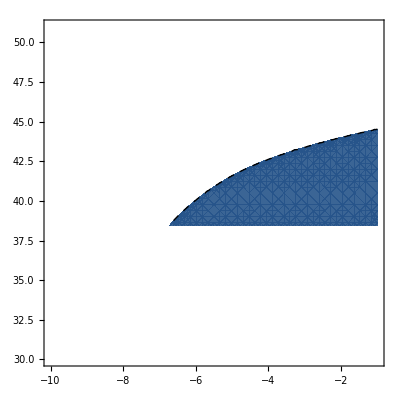

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotQD=ContourPlot[EnergyDiffF[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15),{λ,Log10[10^-10],Log10[10^-1]},{A2,Log10[10^30],Log10[10^51]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.9,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

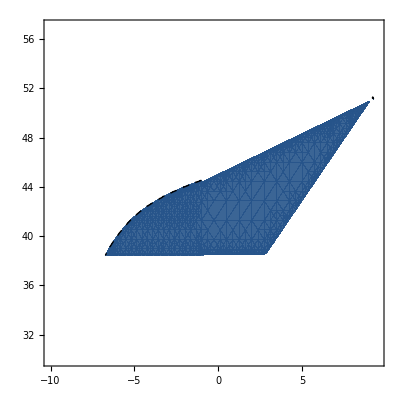

```mathematica
FermiFull=Show[PlotQC,PlotQD]
```

### Exclusion plot β = 1 - Micron screening - compute correct points along exclusion line

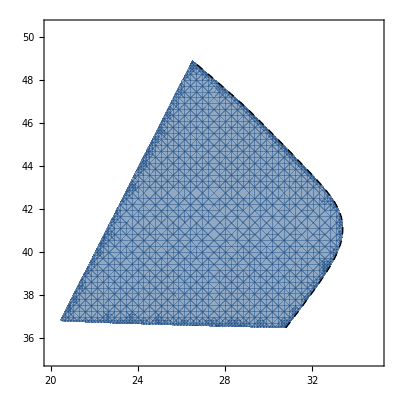

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotF1=ContourPlot[EnergyDiffM[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15),{λ,Log10[10^20],Log10[10^35]},{A2,Log10[10^35],Log10[10^50.5]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.5,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

#### Compute points along exclusion line

```mathematica
λ=10^SetPrecision[32.5,100];
A2=10^SetPrecision[43,100];(*2*10^-21 liegt bei ~43*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

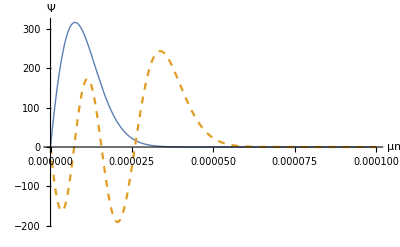

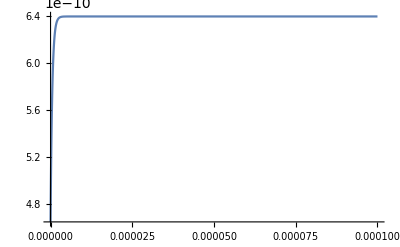

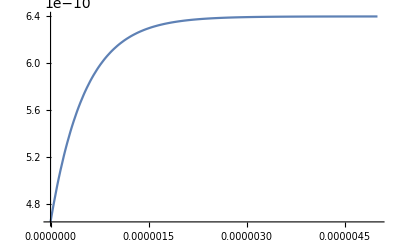

1.261673380404653535297717

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[32,100];
A2=10^SetPrecision[44,100];(*2*10^-21 liegt zwischen 43.5 und 44*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

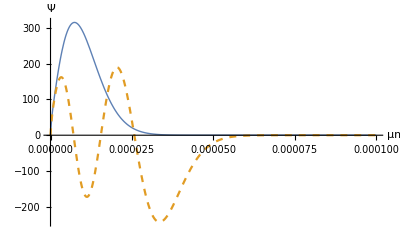

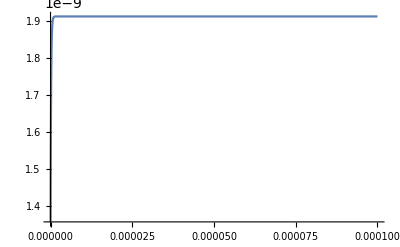

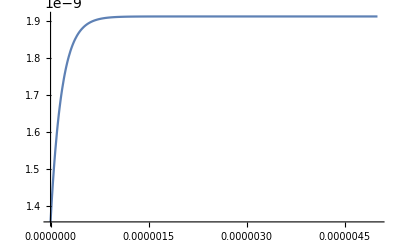

0.440259791026012911594278

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[31.5,100];
A2=10^SetPrecision[45.5,100];(*2*10^-21 liegt zwischen 45 und 45.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=6*10^-7;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

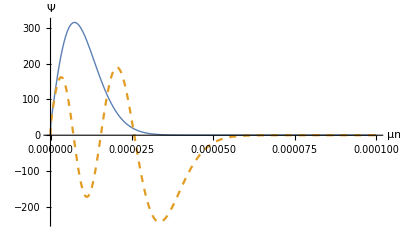

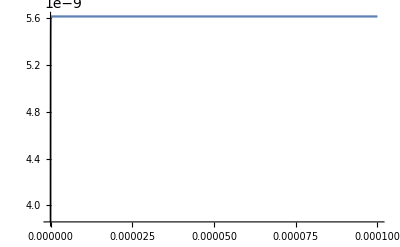

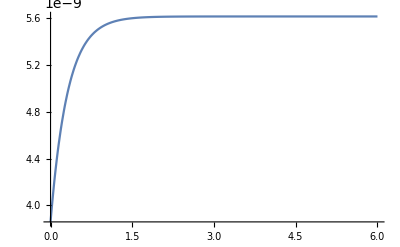

0.016710701061919554442

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[31,100];
A2=10^SetPrecision[47.5,100];(*2*10^-21 liegt zwischen 47 und 47.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=6*10^-8;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

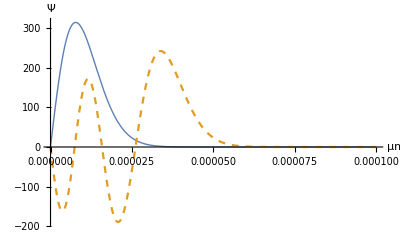

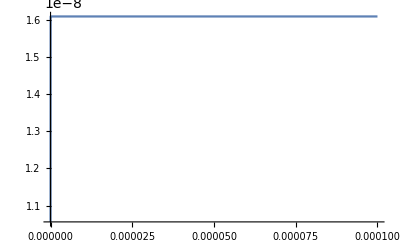

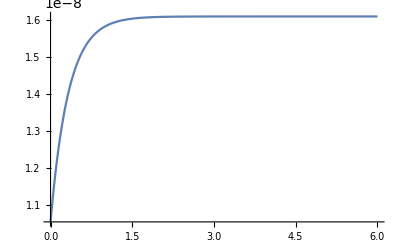

0.23042038010896934832

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[30.5,100];
A2=10^SetPrecision[48.5,100];(*2*10^-21 liegt zwischen 48 und 48.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=3*10^-8;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

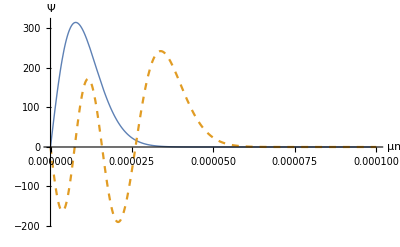

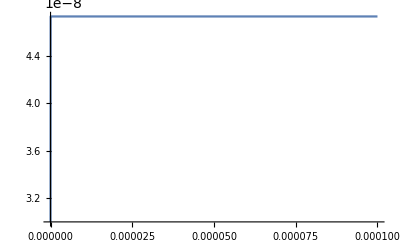

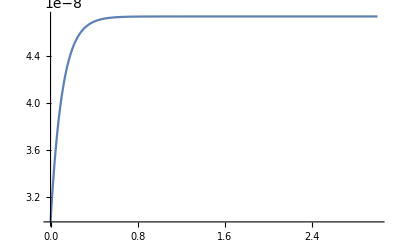

0.2329447824548347892

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[30,100];
A2=10^SetPrecision[49.5,100];(*2*10^-21 liegt zwischen 49 und 49.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-9;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

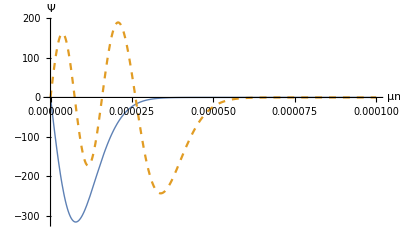

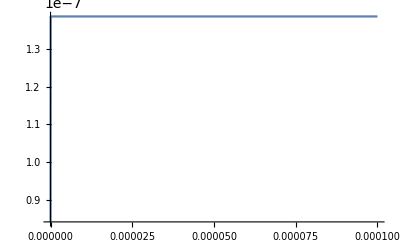

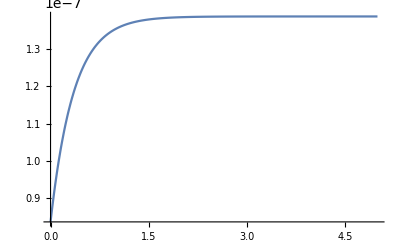

0.235767341641737793

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[29.5,100];
A2=10^SetPrecision[51,100];(*2*10^-21 liegt zwischen 50.5 und 51*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-9;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

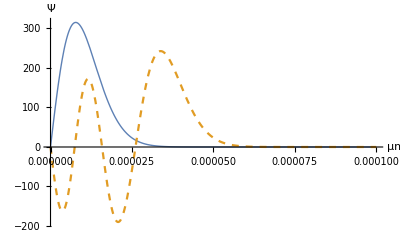

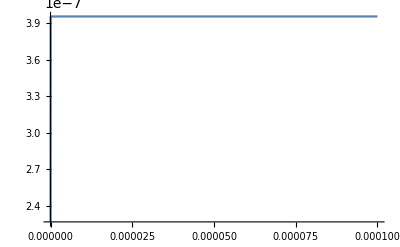

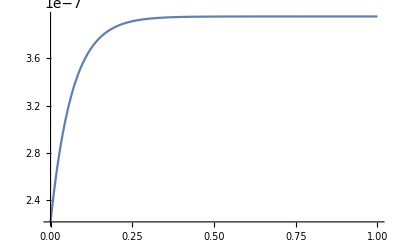

0.23632626395778046

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[29,100];
A2=10^SetPrecision[51.5,100];(*2*10^-21 liegt zwischen 51 und 51.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-10;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

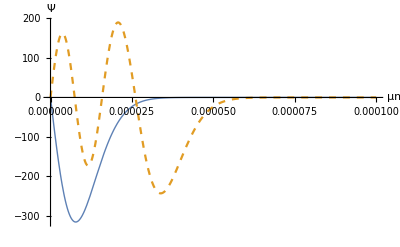

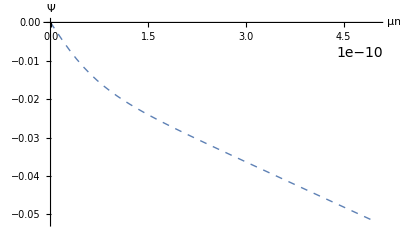

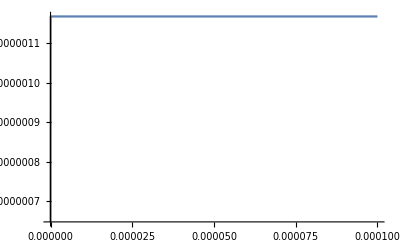

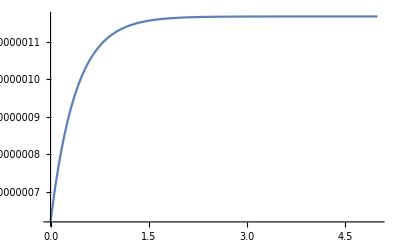

0.2363832641612906

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[28.5,100];
A2=10^SetPrecision[52.5,100];(*2*10^-21 liegt zwischen 52 und 52.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-10;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

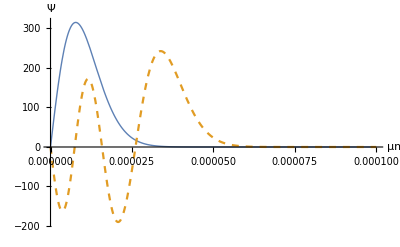

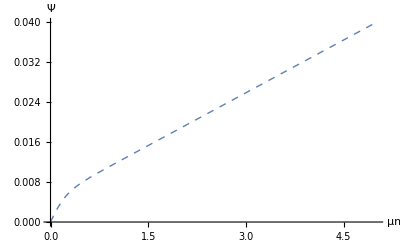

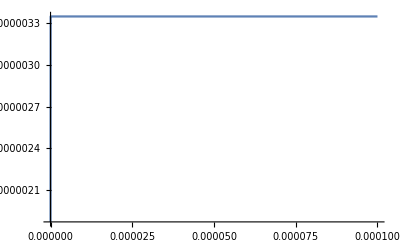

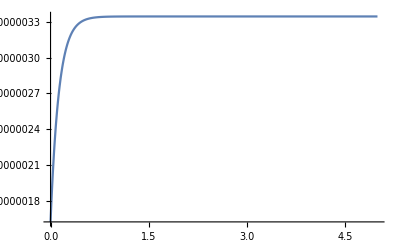

0.236390850214186

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[28,100];
A2=10^SetPrecision[53.5,100];(*2*10^-21 liegt zwischen 53 und 53.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-10;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

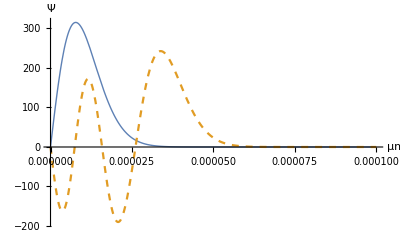

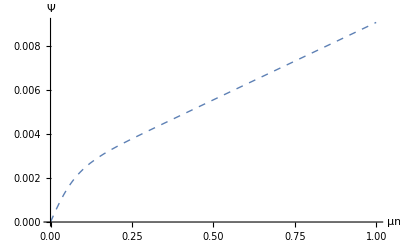

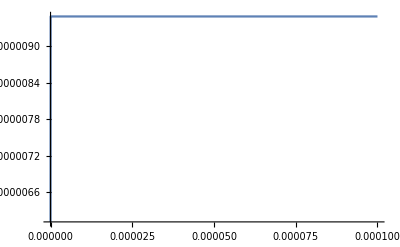

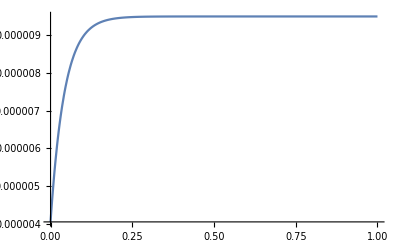

0.23644525612318

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[27.5,100];
A2=10^SetPrecision[54.5,100];(*2*10^-21 liegt zwischen 54 und 54.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-11;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

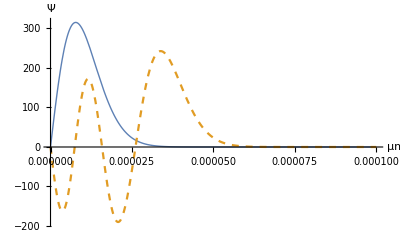

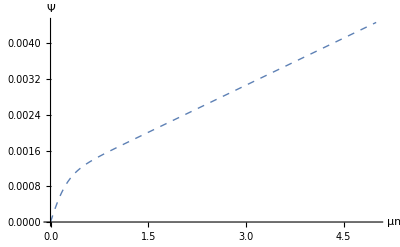

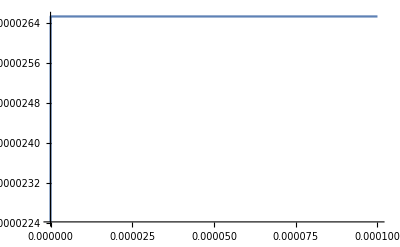

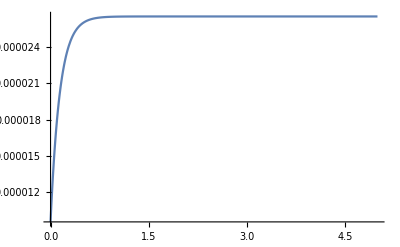

0.2364525374909

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[27,100];
A2=10^SetPrecision[55.5,100];(*2*10^-21 liegt zwischen 55 und 55.5*)
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-11;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

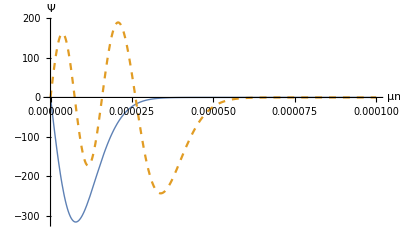

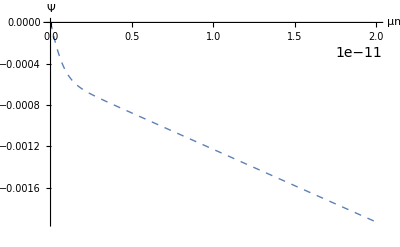

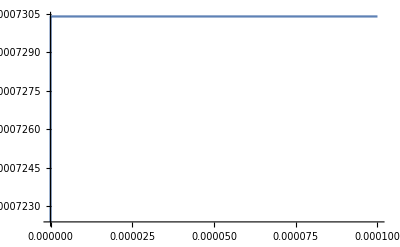

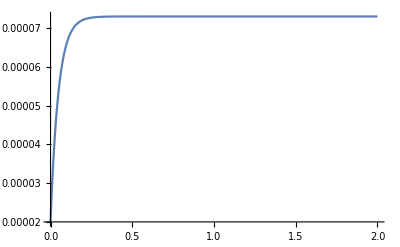

0.236456770029

```mathematica
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[{f1[z]},{z,0,Cutoff2},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

#### Final exclusion plot

{{27,55.5},{27.5,54.5},{28,53.5},{28.5,52.5},{29,51.5},{29.5,51},{30,49.5},{30.5,48.5},{31,47.5},{31.5,45.5},{32,44},{32.5,43}}

InterpolatingFunction[…]

117.01-2.26224 x

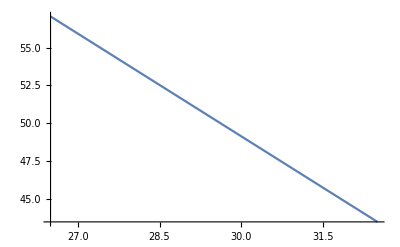

```mathematica
ExculsionLine={{27,55.5},{27.5,54.5},{28,53.5},{28.5,52.5},{29,51.5},{29.5,51},{30,49.5},{30.5,48.5},{31,47.5},{31.5,45.5},{32,44},{32.5,43}}
f=Interpolation[ExculsionLine,InterpolationOrder->3]
FIT2[x_]:=117.01-2.262237762237765 x
f3=Fit[ExculsionLine,{1,x},x]
Clear[Exclude]
Exclude2[λ_,A2_,β_]:=If[FIT2[Log10[λ]]>Log10[A2]&&(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)<0.1,10,0]
Plot[FIT2[λ],{λ,26.5,32.5}]
```

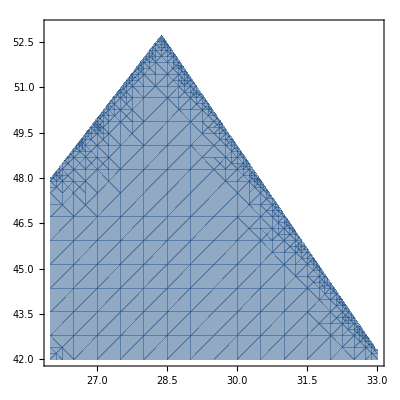

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotF2=ContourPlot[Exclude2[10^λ,10^A2,β],{λ,Log10[10^26],Log10[10^33]},{A2,Log10[10^42],Log10[10^53]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.5,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

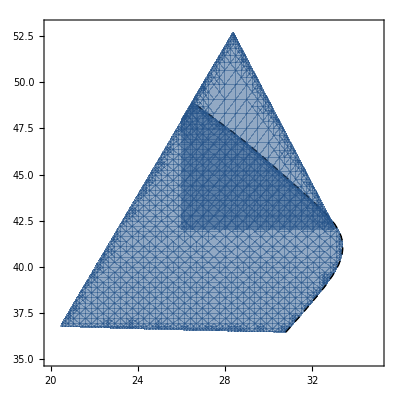

```mathematica
Micron1=Show[PlotF1,PlotF2]
```

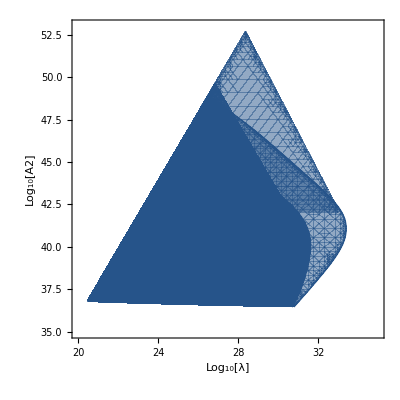

```mathematica
Show[Fermi1,Micron1]
```

### Exclusion plot β = 1 - Micron screening second part (exp ~1)

#### Compute points along exclusion line

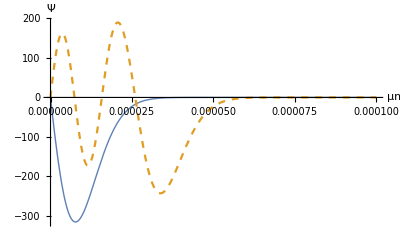

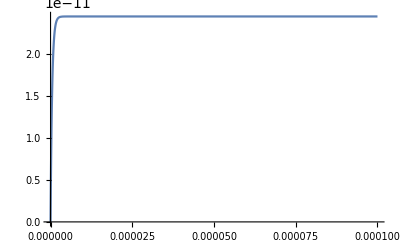

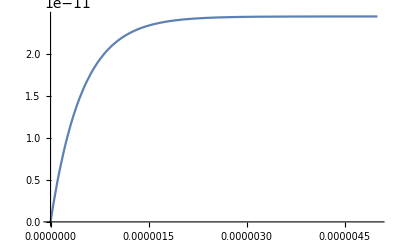

0.5096620795214756272994653

0.374578213935570262592814146578

```mathematica
λ=10^SetPrecision[-3,100];
A2=10^SetPrecision[45,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

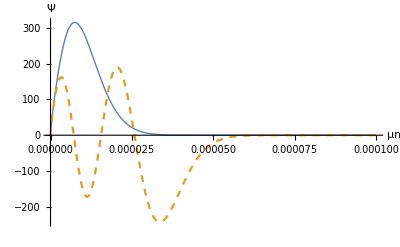

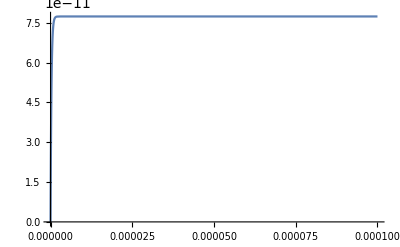

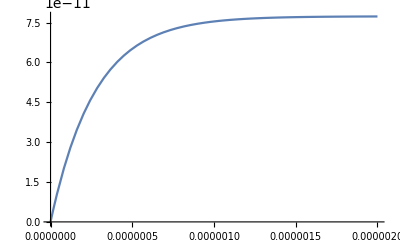

0.208306669979989780697966

0.447618904344124331450564030269

```mathematica
λ=10^SetPrecision[-2,100];
A2=10^SetPrecision[45.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

```mathematica
λ=10^SetPrecision[-1,100];
A2=10^SetPrecision[46.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-6;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.733958708705838384191633

0.00491946449963245811113388467277

```mathematica
λ=10^SetPrecision[0,100];
A2=10^SetPrecision[47,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.78757170981956408959227

0.00494766555032134277754943702939

```mathematica
λ=10^SetPrecision[1,100];
A2=10^SetPrecision[48,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-7;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.8846466429727098013517

0.0000464643074635387617577174963713

```mathematica
λ=10^SetPrecision[2,100];
A2=10^SetPrecision[49,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-8;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.9237211794811112368977

3.05645647570965224128115190508×10^-7

```mathematica
λ=10^SetPrecision[3,100];
A2=10^SetPrecision[49.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=2*10^-8;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.93644810002073920916

2.00852042464580491152307365617×10^-7

```mathematica
λ=10^SetPrecision[4,100];
A2=10^SetPrecision[50.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1*10^-8;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.941754922103133691665

7.16716377288084368897747955251×10^-10

```mathematica
λ=10^SetPrecision[5,100];
A2=10^SetPrecision[51,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=3*10^-9;

POINTS1=300; (*Set number of points for equidistant grid*)
POINTS2=300;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.65600340687026127754

4.12323508554784492814306620728×10^-10

```mathematica
λ=10^SetPrecision[6,100];
A2=10^SetPrecision[52,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=8*10^-10;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.94641542361000783715

1.32967541475775910091181667813×10^-12

```mathematica
λ=10^SetPrecision[7,100];
A2=10^SetPrecision[52.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=5*10^-10;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.9456717446992546295

7.50667324022073190097239767955×10^-13

```mathematica
λ=10^SetPrecision[8,100];
A2=10^SetPrecision[53.5,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=3*10^-10;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.9467273922238644869

2.38197521116213918285990627008×10^-15

```mathematica
λ=10^SetPrecision[9,100];
A2=10^SetPrecision[54,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1.5*10^-10;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
Abs[EnergyDiffM[1,4,λ,A2,β]/(2*10^-21)]
```

-Graphics-

-Graphics-

-Graphics-

0.9468048906710111

1.34041150452435127474391426922×10^-15

```mathematica
λ=10^SetPrecision[10,100];
A2=10^SetPrecision[55,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=3*10^-11;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)
```

-Graphics-

-Graphics-

-Graphics-

0.946866231347770139

0.0005043716361511328165888200061810944272007779299862787282500815545670489724267893151362497521454764

```mathematica
λ=10^SetPrecision[11,100];
A2=10^SetPrecision[56,100];
β=10^0;
Cutoff1=100*10^-6;
Cutoff2=1.5*10^-11;

POINTS1=250; (*Set number of points for equidistant grid*)
POINTS2=250;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];

Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full]

Abs[EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4)]/(2*10^-21)
(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)
```

-Graphics-

-Graphics-

-Graphics-

0.946877229094184772

0.005043716361511328156769908259229939271161446914335130146136191008042502423177327490001912081939362

#### Final exclusion plot

```mathematica
ExculsionLine={{-3,45},{-2,45.5},{-1,46.5},{0,47},{1,48},{2,49},{3,49.5},{4,50.5},{5,51},{6,52},{7,52.5},{8,53.5},{9,54},{10,55},{11,56}};
f2=Fit[ExculsionLine,{1,x},x];
FIT[x_]:=47.21190476190478+0.7803571428571413 x

Plot[FIT[λ],{λ,-3,11}]
Clear[Exclude]
Exclude[λ_,A2_,β_]:=If[FIT[Log10[λ]]>Log10[A2]&&(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)<0.1&&RangeV2[λ,A2,β]<10^3,10,0]
```

-Graphics-

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@0;
PlotB=ContourPlot[Exclude[10^λ,10^A2,β],{λ,Log10[10^-3],Log10[10^12]},{A2,Log10[10^35],Log10[10^57]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

-Graphics-

```mathematica
PlotQA=ContourPlot[EnergyDiffM[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15),{λ,Log10[10^-10],Log10[10^-2]},{A2,Log10[10^30],Log10[10^51]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

-Graphics-

```mathematica
MicronFull=Show[PlotQA,PlotB]
```

-Graphics-

```mathematica
FULLQ=Show[MicronFull,FermiFull]
```

-Graphics-

```mathematica
Export["FULLQ.png",FULLQ,ImageResolution->400];
```

### Exclusion plot for β = 10^18 - Fermi screening

```mathematica
(*Note that in this case perturbation theory is applicable over the remaining non trivial edge of the exclsion plot and no simulations are needed*)
```

```mathematica
Clear[Y,β]
β=10^18;
Y=ColorData["M10DefaultDensityGradient"]@(18/27);
PlotFermi9=ContourPlot[Abs[EnergyDiffF[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15)],{λ,Log10[10^25],Log10[10^33]},{A2,Log10[10^16],Log10[10^27]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[1,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"}),WorkingPrecision->30]
```

-Graphics-

### Exclusion plot for β = 10^18 - Micron screening

```mathematica
(*Note that perturbation theory is valid at the right edge up to ~ λ = 10^32.75, Subscript[A, 2] = 10^26.5, the point at the upper edge (10^32.2,  10^28.7) agrees very well with a simulation, which is why I can use the plot as it is*)
```

```mathematica
Clear[Y,β]
β=10^18;
Y=ColorData["M10DefaultDensityGradient"]@(18/27);
PlotMicron9=ContourPlot[Abs[EnergyDiffM[4,1,10^λ,10^A2,β]/(10^-6*2*10^-15)],{λ,Log10[10^25],Log10[10^35]},{A2,Log10[10^16],Log10[10^35]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.5,Y]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"}),WorkingPrecision->30]
```

-Graphics-

```mathematica
Show[PlotQ1,PlotF1,PlotQ3,PlotQ4]
```

-Graphics-

```mathematica
NewFULL=Show[Micron1,Fermi1,PlotQ3,PlotQ4]
```

-Graphics-

```mathematica
CompNPer=Show[Fermi1,PlotQ1]
Show[PlotQ1]
```

-Graphics-

-Graphics-

```mathematica
Export["CompNPer.png",CompNPer,ImageResolution->400];
```

```mathematica
Export["NewFULL.png",NewFULL,ImageResolution->400];
```

```mathematica
λ=10^SetPrecision[32.2,100];
A2=10^SetPrecision[27,100];(*2*10^-21 liegt zwischen 26.7 und 27.5, cut off von quadratischem Term kommt schon davor*)
β=10^18;
Cutoff1=100*10^-6;
Cutoff2=5*10^-6;

POINTS1=500; (*Set number of points for equidistant grid*)
POINTS2=150;
{points,H,L}=GetMatricesM[λ,A2,β,Cutoff1,Cutoff2,POINTS1,POINTS2];
EVS=Eigensystem[H];
```

```mathematica
RangeV2[λ,A2,β] (*Range in μm, the dilaton gradient is caputured, which I show by plotting the range in μm, but not shown by Mathematica anymore since the field varies so little that is is plotted as constant everywhere *)
Clear[Func,f1,f4,Func2]
F1=Inverse[L].EVS[[-1]][[-1]];
F4=Inverse[L].EVS[[-1]][[-4]];

Clear[Func,f1,f4,Func2]
Func={{0,0}};
Func2={{0,0}};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],F1[[i]]}];
AppendTo[Func2,{points[[i]],F4[[i]]}]]

f1=Interpolation[Func,InterpolationOrder->1];
f4=Interpolation[Func2,InterpolationOrder->1];
Plot[{f1[z],-f4[z]},{z,0,Cutoff1},PlotRange->Full,PlotStyle->{Thick,Dashed},AxesLabel->{"μm","Ψ"}] 

Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff1},PlotRange->Full,WorkingPrecision->30]
Plot[ϕI[λ,ρM,A2,β,z*m2invMeV],{z,0,Cutoff2},PlotRange->Full,WorkingPrecision->30]

Abs[(EVS[[1]][[-1]]-E1-(EVS[[1]][[-4]]-E4))/(2*10^-21)]
```

0.3173852935970823808722752900821411201712310564548973013154686353798528760240392816611190430070747410124132112784614649075723322915856838235018731643049117362032178552366623564815502846369116324614062236060603774453264362159100347401057289279336596746012289453665741603124308210679439607978291406367471139764733026694468327261975729914076928568778746927834454508962267518678218269333233524170196803003839384934639811557540234519856397109551016114838065581683826329451763930412306669832734813240155123306350096875766379967350892177420769936289712243267309927169334952783680179649444758665361404536989159387208811638563683450562272756947669953192743380116869999341924981983920797371512047952471770155506589852345548927272924581198812236802844093623844045267309653185258338231991482203107055160437398088589512700864461965467582495246354230256149857133443302475075326545595083159065137862771121398034994247878260647509108972066278187216813318585071599696019615772281493485562334768426247099039752834765825

-Graphics-

-Graphics-

-Graphics-

1.619093072996850465165379